The following codes shall only be run once!!!

```mathematica
Clear["Global`*"]
Needs["Developer`"]
Needs["CCompilerDriver`"]
$LibraryPath=AppendTo[$LibraryPath,FileNameJoin[{NotebookDirectory[],"../MLL-lib"}]];
ClearAll[LegendreRuleMLL,DunavantRuleMLL]
LegendreRuleMLL=LibraryFunctionLoad["lib-franklin","LegendreRule_MLL",{Integer,Real,Real},{Real,2,"Shared"}];
DunavantRuleMLL=LibraryFunctionLoad["lib-franklin","DunavantRule_MLL",{Integer,{Real,2,"Constant"}},{Real,2,"Shared"}];
(*
SetDirectory[FileNameJoin[{NotebookDirectory[],"../ML-exe"}]];
Install["DunavantRule.exe"];
Install["LegendreRule.exe"];
(*Install More Executables Here...*)
ResetDirectory[];
*)
```

## Quadrature Rules and Numerical Integration - Modular

### Single Triangle

```mathematica
ClearAll[LegendreRule,DunavantRule]
LegendreRule[order_,xmin_,xmax_]:=LegendreRuleMLL[order,xmin,xmax]//Quiet;
DunavantRule[rule_,p_]:=Module[{qx,qy,q,w},
{qx,qy,w}=DunavantRuleMLL[rule,p]//Quiet;
q={qx,qy}ᵀ//ToPackedArray;
w=w//ToPackedArray;
{q,w}
]
ClearAll[QuadratureProduct2D]
QuadratureProduct2D[{q1_, w1_}, {q2_, w2_}] := Module[{q,w},
q=Outer[{#1,#2}&,q1,q2]//Flatten[#,1]&//N//ToPackedArray;
w=Outer[Times,w1,w2]//Flatten[#,1]&//N//ToPackedArray;
{q,w}
]
ClearAll[NIntegrateDuffyTriangle,NIntegrateNonSingularTriangle]
NIntegrateDuffyTriangle[p_,fun_,{q_,w_}]:=
Module[{qq,ww,P0P1,P1P2,P1P2Sq,λ1,λ2,A,b,n,DetA},
P0P1=p⟦2⟧-p⟦1⟧;
P1P2=p⟦3⟧-p⟦2⟧;
A={P0P1,P1P2}//Transpose;
DetA=Abs[Det[A]];
b=p⟦1⟧;
n=Length[q];
P1P2Sq=Total[P1P2^2];
λ1=P0P1.P1P2/P1P2Sq;
λ2=DetA/P1P2Sq;
qq=A.{#⟦1⟧,#⟦1⟧#⟦2⟧}+b&/@q;
ww=Table[w⟦i⟧/Sqrt[(q⟦i,2⟧+λ1)^2+λ2^2],{i,n}];
DetA/Sqrt[P1P2Sq]*∑_(i=1)^n ww⟦i⟧fun[qq⟦i⟧]
]
NIntegrateNonSingularTriangle[p_,fun_,{q_,w_}]:=
Module[{n,A,b,AreaOver2,qq},
n=Length[q];
A={p⟦3⟧-p⟦1⟧,p⟦2⟧-p⟦1⟧}ᵀ;
b=p⟦2⟧+p⟦3⟧;
AreaOver2=0.25*Abs[Det[A]];
qq=0.5*(A.#+b&/@q);
AreaOver2∑_(i=1)^n w⟦i⟧fun[qq⟦i⟧]
]

ClearAll[NIntegrateArcSinhTriangle]
NIntegrateArcSinhTriangle[P_,fun_,{{ξu_,wu_},{ξv_,wv_}}]:=
Module[{P0P1,P0P2,P1P2,LP1P2,uP1P2,h,Ah,x1p,x2p,uL,uU,vL,vU,xyij,Wij,Nij},
P0P1=P⟦2⟧-P⟦1⟧;
P0P2=P⟦3⟧-P⟦1⟧;
P1P2=P⟦3⟧-P⟦2⟧;
LP1P2=Norm[P1P2];
uP1P2=P1P2/LP1P2;
h=(-P1P2⟦1⟧P⟦1,2⟧+P0P2⟦1⟧P⟦2,2⟧-P0P1⟦1⟧P⟦3,2⟧)/LP1P2;
x1p=P0P1.uP1P2//N;
x2p=P0P2.uP1P2//N;
uL=ArcSinh[x1p/h];
uU=ArcSinh[x2p/h];
vL=0;
vU=h;
Ah=h({{uP1P2⟦1⟧, -uP1P2⟦2⟧}, {uP1P2⟦2⟧, uP1P2⟦1⟧}});
xyij=Outer[{#2Sinh[uL+(uU-uL)#1],#2}&,ξu,ξv]//Flatten[#,1]&//Map[P⟦1⟧+Ah.#&,#]&;
Wij=Outer[Times,wu,wv]//Flatten[#,1]&;
Nij=Length[wu]Length[wv];
Abs[h(uU-uL)]∑_(k=1)^Nij Wij⟦k⟧fun[xyij⟦k⟧]
]
```

Arcsinh transform

```mathematica
ClearAll[P,fun,x,y,a0]
P={{3,2},{1,0},{0,2}};
fun[{x_,y_}]:=x^3+y^3;
a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-P⟦1⟧],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->20];
data=Table[a1=NIntegrateArcSinhTriangle[P,fun,{LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]}];
{Nu,Nv,-Log@Abs[(a1-a0)/a0]/Log[10]}
,{Nu,10},{Nv,10}]//Flatten[#,1]&;
ListPlot3D[data,AxesLabel->{"Nu","Nv","# of significant digits"},PlotLabel->fun[{x,y}],ImageSize->Large]
```

-Graphics3D-

Compute the near singular integral over the triangle using Duffy transform
	(1,0),(0,2),(3,2)

```mathematica
ClearAll[p,fun,a0,x,y]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=x;
Print["true value = ",a0=NIntegrate[fun[{x,y}]/Norm[{x,y}-p⟦1⟧],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->25]];
Module[{q,w},
Table[
{q,w}=QuadratureProduct2D[LegendreRule[n1,0,1],LegendreRule[n2,0,1]];
-Log@Abs[(NIntegrateDuffyTriangle[p,fun,{q,w}]-a0)/a0]/Log[10],
{n1,15},{n2,15}]//ListPlot3D[#,AxesLabel->{"n1","n2","# of significant digits"},PlotLabel->fun[{x,y}],ImageSize->Large,PlotRange->All]&//Print
];
```

true value = 3.317529971404693346797939

-Graphics3D-

Compute the non-singular integral over the triangle using Dunavant rule:
	(1,0),(0,2),(3,2)

true value = 2.4905602857143116709×10^7

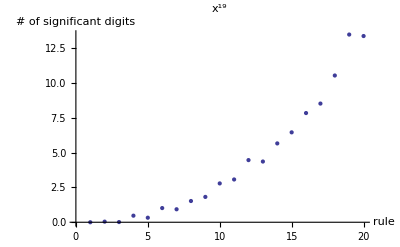

```mathematica
ClearAll[p,fun,a0,x,y]
p={{1,0},{0,2},{3,2}};
fun[{x_,y_}]:=x^19;
Print["true value = ",a0=NIntegrate[fun[{x,y}],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->20]];
Module[{q,w,pStd},
pStd={{-1,-1},{-1,1},{1,-1}};
Table[
{q,w}=DunavantRule[rule,pStd];
-Log@Abs[(NIntegrateNonSingularTriangle[p,fun,{q,w}]-a0)/a0]/Log[10],
{rule,1,20}
]//ListPlot[#,AxesLabel->{"rule","# of significant digits"},AxesOrigin->{0,0},PlotLabel->fun[{x,y}]]&//Print
];
```

### Near-Singular

Mathematical value=3530.779045206299

true value=3530.78

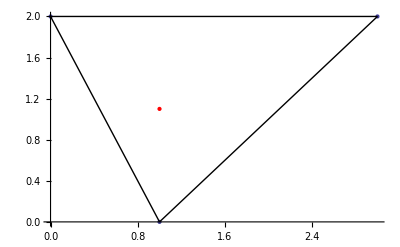

-Graphics3D-

```mathematica
ClearAll[P, P0, s1, s2, s3, s12, s23, s31, wP, quadrules, iP]
P = {{1, 0}, {0, 2}, {3, 2}} // N // ToPackedArray;
P0 = {1,1.1} // N // ToPackedArray;
s1 = Det[{P[[1]] - P0, P[[2]] - P[[1]]}];
s2 = Det[{P[[2]] - P0, P[[3]] - P[[2]]}];
s3 = Det[{P[[3]] - P0, P[[1]] - P[[3]]}];
s12 = s1 s2;
s23 = s2 s3;
s31 = s3 s1;
wP = {1, 1, 1} // N // ToPackedArray;
If[s12 >= 0 && s23 >= 0 && s31 >= 0, ,
  If[s12 > 0, wP[[3]] = -1.0,
    If[s23 > 0, wP[[1]] = -1.0,
      wP[[2]] = -1.0
      ];
    ];
  ];
ClearAll[fun, x, y, a0,a00]
fun[{x_, y_}] := x^10 + 2y^10;
raw = Table[
   quadrules = {LegendreRule[Nu, 0, 1], LegendreRule[Nv, 0, 1]};
   iP =
    {NIntegrateArcSinhTriangle[{P0, P[[1]], P[[2]]}, fun, quadrules],
     NIntegrateArcSinhTriangle[{P0, P[[2]], P[[3]]}, fun, quadrules],
     NIntegrateArcSinhTriangle[{P0, P[[3]], P[[1]]}, fun, quadrules]};
   a1 = iP.wP;
   {Nu, Nv, a1}
   ,
   {Nu, 20}, {Nv, 20}];
a00=NIntegrate[fun[{x,y}]/Norm[{x,y}-P0],{y,0,2},{x,1-y/2,1+y},WorkingPrecision->16];
a0 = raw[[20, 20, 3]];
Print["Mathematical value=",a00];
Print["true value=", a0];
data = {#[[1]], #[[2]], -Log@Abs[(#[[3]] - a0)/a0]/Log[10]} & /@ Flatten[raw, 1];
ListPlot[{P, {P0}}, PlotStyle -> {PointSize[Large], Red}, Epilog -> {Black, Line[P], Line[{P[[3]], P[[1]]}]}]
ListPlot3D[data, AxesLabel -> {"Nu", "Nv", "# of significant digits"}, PlotLabel -> fun[{x, y}], ImageSize -> Large]
```

### VscnmFunc

```mathematica
ClearAll[ConstructQuadratureRules,VscnmFunc,VscnmFuncDuffy,VscnmQuadrature]

ConstructQuadratureRules[ruleN_,ruleNp_,{nNpS1_,nNpS2_}]:=
Module[{pStd,qxNpS,qyNpS,wNpS,qNpS},
pStd={{-1,-1},{-1,1},{1,-1}};
{qxNpS,qyNpS,wNpS}=QuadratureProduct2D[LegendreRule[nNpS1,0,1],LegendreRule[nNpS2,0,1]];
qNpS={qxNpS,qyNpS}ᵀ//ToPackedArray;
wNpS=wNpS//ToPackedArray;
{DunavantRule[ruleN,pStd],DunavantRule[ruleNp,pStd],{qNpS,wNpS}}
]
VscnmFunc[m_,r_,rp_]:=Module[{dr,R,Phi},
dr=r-rp;R=Norm[dr];Phi=ArcTan[dr⟦1⟧,dr⟦2⟧];
(*Exp[-ⅈ m Phi]/R*mus[rp]*PhaseFunc[Phi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m Phi]/R*mus[rp]*PhaseFunc[Phi-phis]*Exp[-rp⟦1⟧]
]
VscnmFuncDuffy[m_,r_,rp_]:=With[{Phi=(r-rp)//ArcTan[#⟦1⟧,#⟦2⟧]&},
(*Exp[-ⅈ m Phi]*mus[rp]*PhaseFunc[Phi-phis]*Exp[-OpticalPathC[rp,phis+π]]*)
Exp[-ⅈ m Phi]*mus[rp]*PhaseFunc[Phi-phis]*Exp[-rp⟦1⟧]
]
VscnmQuadrature[n_,m_,{{qN_,wN_},{qNp_,wNp_},{qNpS_,wNpS_}}]:=
Module[{nN,nNp,nNpS,AN,bN,AreaOver2N,qqN,Vscnm,i,r,np,xxN},
nN=Length[qN];
nNp=Length[qNp];
nNpS=Length[qNpS];
AN={pt⟦n,3⟧-pt⟦n,1⟧,pt⟦n,2⟧-pt⟦n,1⟧}ᵀ;
bN=pt⟦n,2⟧+pt⟦n,3⟧;
AreaOver2N=0.25*Abs[Det[AN]];
qqN=0.5*(AN.#+bN&/@qN);
Vscnm=0.0;
For[i=1,i≤nN,i++,
r=qqN⟦i⟧;
xxN=0.0;
For[np=1,np<n,np++,xxN+=NIntegrateNonSingularTriangle[pt⟦np⟧,VscnmFunc[m,r,#]&,{qNp,wNp}];];
For[np=n+1,np≤Ns,np++,xxN+=NIntegrateNonSingularTriangle[pt⟦np⟧,VscnmFunc[m,r,#]&,{qNp,wNp}];];
xxN+=NIntegrateDuffyTriangle[{r,pt⟦n,1⟧,pt⟦n,2⟧},VscnmFuncDuffy[m,r,#]&,{qNpS,wNpS}];
xxN+=NIntegrateDuffyTriangle[{r,pt⟦n,2⟧,pt⟦n,3⟧},VscnmFuncDuffy[m,r,#]&,{qNpS,wNpS}];
xxN+=NIntegrateDuffyTriangle[{r,pt⟦n,3⟧,pt⟦n,1⟧},VscnmFuncDuffy[m,r,#]&,{qNpS,wNpS}];
xxN*=wN⟦i⟧;
Vscnm+=xxN;
];
Vscnm*=AreaOver2N;
Vscnm
]
ClearAll[VscnmQuadratureDebugUse]
VscnmQuadratureDebugUse[n_,m_,ruleN_,ruleNp_,{nNpS1_,nNpS2_}]:=
With[{quadrules=ConstructQuadratureRules[ruleN,ruleNp,{nNpS1,nNpS2}]},VscnmQuadrature[n,m,quadrules]]
```

```mathematica
ClearAll[NIntegrateSingularNearSingularArcSinhTriangle]
NIntegrateSingularNearSingularArcSinhTriangle[P0_,P_,fun_,quadrules_]:=
Module[{ s1, s2, s3, s12, s23, s31, wP, iP,x,y,a0,a00},
s1 = Det[{P[[1]] - P0, P[[2]] - P[[1]]}];
s2 = Det[{P[[2]] - P0, P[[3]] - P[[2]]}];
s3 = Det[{P[[3]] - P0, P[[1]] - P[[3]]}];
s12 = s1 s2;
s23 = s2 s3;
s31 = s3 s1;
wP = {1, 1, 1} // N // ToPackedArray;
If[s12 >= 0 && s23 >= 0 && s31 >= 0, ,
  If[s12 > 0, wP[[3]] = -1.0,
    If[s23 > 0, wP[[1]] = -1.0,
      wP[[2]] = -1.0
      ];
    ];
  ];
iP =
    {NIntegrateArcSinhTriangle[{P0, P[[1]], P[[2]]}, fun, quadrules],
     NIntegrateArcSinhTriangle[{P0, P[[2]], P[[3]]}, fun, quadrules],
     NIntegrateArcSinhTriangle[{P0, P[[3]], P[[1]]}, fun, quadrules]};
iP.wP
];
```

Arcsinh method: Singular and near-singular

In pt⟦np⟧: False

r={0.24,0.76}

cntr⟦np⟧={0.151174,0.758632}

|r-rp|≃0.0888364

best value for m= 0 is: 0.0159878

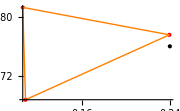

-Graphics3D-

```mathematica
ClearAll[m,np,Nu,Nv,point,a0,a1]
{Nu,Nv}={50,50};
m=0;
np=1;
point={0.24,0.76};
Print["In pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];

a0=NIntegrateSingularNearSingularArcSinhTriangle[point,pt⟦np⟧,VscnmFuncDuffy[m,point,#]&,{LegendreRule[100,0,1],LegendreRule[100,0,1]}];

raw=Table[
a1=NIntegrateSingularNearSingularArcSinhTriangle[point,pt⟦np⟧,VscnmFuncDuffy[m,point,#]&,{LegendreRule[Nu,0,1],LegendreRule[Nv,0,1]}];
{Nu,Nv,a1}
,{Nu,50},{Nv,5}]//Flatten[#,1]&;
data={#⟦1⟧,#⟦2⟧,-Log@Abs[(#⟦3⟧-a0)/a0]/Log[10]}&/@raw;
Print["best value for m= ",m," is: ",a0];
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->Small]
ListPlot3D[data,AxesLabel->{"Nu","Nv","# of significant digits"},ImageSize->Large]
```

Duffy - Only singular

In pt⟦np⟧: True

r={0.16,0.76}

cntr⟦np⟧={0.151174,0.758632}

|r-rp|≃0.00893128

best value for m=0 is: 0.0166193

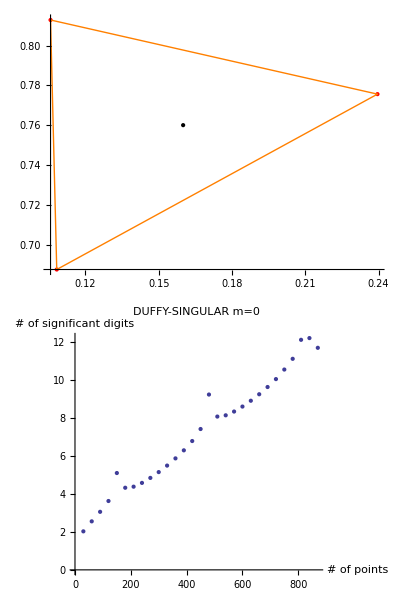

```mathematica
ClearAll[m,np,n1,n2,q,w,point,xx,data]
pStd={{-1,-1},{-1,1},{1,-1}};
{n1,n2}={5,5};
m=0;
np=1;
point={0.16,0.76};
Print["In pt⟦np⟧: ",InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
n2=10;
data=Table[{q,w}=QuadratureProduct2D[LegendreRule[n2,0,1],LegendreRule[n1,0,1]];
xx=0.0;
xx+=NIntegrateDuffyTriangle[{point,pt⟦np,1⟧,pt⟦np,2⟧},VscnmFuncDuffy[m,point,#]&,{q,w}];
xx+=NIntegrateDuffyTriangle[{point,pt⟦np,2⟧,pt⟦np,3⟧},VscnmFuncDuffy[m,point,#]&,{q,w}];
xx+=NIntegrateDuffyTriangle[{point,pt⟦np,3⟧,pt⟦np,1⟧},VscnmFuncDuffy[m,point,#]&,{q,w}];
{3*n2*n1,xx},{n1,30}];
Print["best value for m=",m," is: ",data⟦-1,2⟧];
Print@TableForm@{
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->Small],
({#⟦1⟧,-Log@Abs[#⟦2⟧-data⟦-1,2⟧]/Log[10]}&/@data)//ListPlot[#,PlotLabel->"DUFFY-SINGULAR "<>"m="<>ToString[m],AxesLabel->{"# of points","# of significant digits"},AxesOrigin->{0,0},ImageSize->Medium]&};
```

Dunavant method
Only non-singular

Out of pt⟦np⟧: True

r={0.6,0.358632}

cntr⟦np⟧={0.190092,0.70522}

|r-rp|≃0.536794

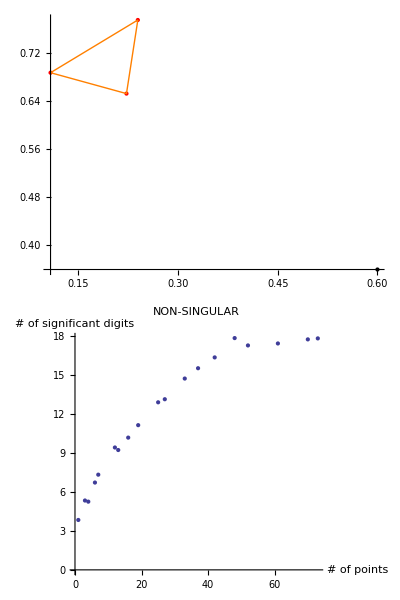

```mathematica
ClearAll[m,np,rule,pStd,point,data,quadrules]
pStd={{-1,-1},{-1,1},{1,-1}};
rule=5;
m=10;
np=2;
point={0.6,0.358632};
Print["Out of pt⟦np⟧: ",!InTriangle[point,pt⟦np⟧]];
Print["r=",point];
Print["cntr⟦np⟧=",cntr⟦np⟧]
Print["|r-rp|≃",cntr⟦np⟧-point//Norm];
data=Table[quadrules=DunavantRule[rule,pStd];{Length[quadrules⟦1⟧],NIntegrateNonSingularTriangle[pt⟦np⟧,VscnmFunc[m,point,#]&,quadrules]},{rule,1,20}];
Print@TableForm@{
ListPlot[{pt⟦np⟧,{point}},PlotStyle->{{Red,PointSize[Large]},{Black,PointSize[Large]}},Epilog->{Orange,Line[pt⟦np⟧],Line[{pt⟦np,1⟧,pt⟦np,3⟧}]},ImageSize->Small],
({#⟦1⟧,-Log@Abs[#⟦2⟧-data⟦-1,2⟧]/Log[10]}&/@data)//ListPlot[#,PlotLabel->"NON-SINGULAR",AxesLabel->{"# of points","# of significant digits"},AxesOrigin->{0,0},ImageSize->Medium]&};
```

## Dumping and Reading .msh File - Modular

```mathematica
Needs["Developer`"]
```

```mathematica
ClearAll[sprtr,ReadMSHFile,DumpMSHFileTo2DATFiles,ReadMSHFileFrom2DATFiles]
If[$OperatingSystem=="MacOSX",sprtr="_";,0.0];
If[$OperatingSystem=="Windows",sprtr="_";,0.0];
If[$OperatingSystem=="Linux",sprtr="_";,0.0];

ReadMSHFile[filename_]:=Module[{i,SkipStreamNumbers,ReadStreamNumbers,meshStr,nNodes,nodesTable,nElements,nPoints,nLines,nTriangles,trianglesTable,temp},
SkipStreamNumbers=Skip[#1,Table[Number,{i,Range[#2]}]]&;
ReadStreamNumbers=Read[#1,Table[Number,{i,Range[#2]}]]&;
meshStr=OpenRead[filename];
Find[meshStr,"$Nodes"];
nNodes=Read[meshStr,Number];
nodesTable=ConstantArray[0.0,{nNodes,2}];
For[i=1,i≤nNodes,i++,
Skip[meshStr,Number];
nodesTable⟦i⟧=N@ReadStreamNumbers[meshStr,2];
Skip[meshStr,Number];
];
Find[meshStr,"$Elements"];
nElements=Read[meshStr,Number];
nPoints=0;nLines=0;nTriangles=0;
trianglesTable=ConstantArray[0.0,{nElements,3}];
For[i=1,i≤nElements,i++,
Skip[meshStr,Number];
temp=Read[meshStr,Number];
If[temp==15,nPoints++;SkipStreamNumbers[meshStr,4];];
If[temp==1,nLines++;SkipStreamNumbers[meshStr,5];];
If[temp==2,nTriangles++;SkipStreamNumbers[meshStr,3];trianglesTable⟦nTriangles⟧=N@ReadStreamNumbers[meshStr,3];];
];
trianglesTable=trianglesTable⟦1;;nTriangles⟧;
Close[meshStr];
ToPackedArray/@{nodesTable,Floor@trianglesTable}
]
DumpMSHFileTo2DATFiles[mshfilename_]:=Module[{dir,nodesTable,trianglesTable},
{nodesTable,trianglesTable}=ReadMSHFile[mshfilename];
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
CreateDirectory[dir]//Quiet;
Print["directory created:",dir];
Export[FileNameJoin[{dir,"nodes.dat"}],nodesTable];
Export[FileNameJoin[{dir,"triangles.dat"}],trianglesTable];
Print["exported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["exported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
]
ReadMSHFileFrom2DATFiles[mshfilename_]:=Module[{dir},
dir=FileNameJoin[{DirectoryName[mshfilename],FileBaseName[mshfilename]<>sprtr<>"dat"}];
Print["imported nodes file: ",FileNameJoin[{dir,"nodes.dat"}]];
Print["imported triangles file: ",FileNameJoin[{dir,"triangles.dat"}]];
ToPackedArray/@{N@Import[FileNameJoin[{dir,"nodes.dat"}]],Import[FileNameJoin[{dir,"triangles.dat"}]]}
]
```

Read directly from the .msh file and check

```mathematica
dir=FileNameJoin[{NotebookDirectory[],"mesh"}]
```

/Users/qzmfrank/Codes/rte2dvis/notebook/mesh

```mathematica
{nodesRaw,trianglesRaw}=ReadMSHFile[FileNameJoin[{dir,"trial.msh"}]];
PackedArrayQ/@{nodesRaw,trianglesRaw}
```

OpenRead::noopen: Cannot open "/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial.msh".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 2}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 3}].

ConstantArray::argt: ConstantArray called with 0 arguments; 2 or 3 arguments are expected.

{False,False}

Dump the .msh file data into two separate .dat files

```mathematica
DumpMSHFileTo2DATFiles[FileNameJoin[{dir,"square26.msh"}]]
```

OpenRead::noopen: Cannot open "/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26.msh".

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 2}].

General::stream: $Failed is not a string, InputStream[ ], or OutputStream[ ].

General::stop: Further output of General :: stream will be suppressed during this calculation.

ConstantArray::ilsmn: Single or list of non-negative machine-sized integers expected at position 2 of ConstantArray[0., {Read[$Failed, Number], 3}].

ConstantArray::argt: ConstantArray called with 0 arguments; 2 or 3 arguments are expected.

directory created:/Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat

exported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat/nodes.dat

exported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/square26_dat/triangles.dat

Read the two .dat files and check

```mathematica
{nodesRaw2,trianglesRaw2}=ReadMSHFileFrom2DATFiles[FileNameJoin[{dir,"trial.msh"}]];
PackedArrayQ/@{nodesRaw2,trianglesRaw2}
Total[Norm/@#]&/@{nodesRaw2-nodesRaw,trianglesRaw2-trianglesRaw}
```

imported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial_dat/nodes.dat

imported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/mesh/trial_dat/triangles.dat

Import::nffil: File not found during Import.

{False,False}

{Norm[$Failed]+Norm[-ConstantArray[0.,{Read[$Failed,Number],2}]],Norm[$Failed]+Norm[-Floor[ConstantArray[]]]}

## Direct Integral Solver - Sequential, Interpretive and Partially Compiled

```mathematica
Needs["Developer`"]

ClearAll[filename,mus,mua,mut,g,Phasef,Phasef1,Phasef2,PhaseFunc,PhaseFunc1,phis,Nd]
(*filename=FileNameJoin[{NotebookDirectory[],"../msh","t4.msh"}];*)
filename=FileNameJoin[{NotebookDirectory[],"../msh","square162.msh"}];
DumpMSHFileTo2DATFiles[filename];
mus[{x_,y_}]:=0.5Log[2.0]
mua[{x_,y_}]:=Log[2.0]
mut[{x_,y_}]:=mua[{x,y}]+mus[{x,y}]
g=0.6;
Phasef1[m_]:=g^Abs[m]
Phasef2[m_]:=If[m==0,1.0,0.0]
Phasef=Phasef1;
PhaseFunc1=Compile[{{phi,_Real}},(1.0-g^2)/(2π(1+g^2-2g Cos[phi])),CompilationTarget:>"C"];
PhaseFunc=PhaseFunc1;
phis=0;
Nd=10;

ClearAll[iG,iL,Rank,ToCmplxPckdArry]
iG[{n_,m_},{Ns_,Nd_}]:=(n-1)*(2Nd+1)+m+Nd+1
iL[ng_,{Ns_,Nd_}]:={IntegerPart[(ng-1)/(2Nd+1)+1],Mod[ng-Nd-1,(2Nd+1),-Nd]}
Rank[x_]:=Length/@{x,xᵀ}//Quiet
ToCmplxPckdArry=ToPackedArray[N[Re[#]]]+ⅈ ToPackedArray[N[Im[#]]]&;

ClearAll[TriPtPreCalc,CntrPreCalc,r2rXYPreCalc,r2rRPreCalc,r2rPhiPreCalc,r2rFPreCalc,AreaPreCalc]
TriPtPreCalc[p_,t_]:=p⟦#⟧&/@t//ToPackedArray
CntrPreCalc[pt_]:=(Total/@pt)/3.0//ToPackedArray
r2rXYPreCalc[cntr_]:=Outer[If[#1<#2,Subtract@@cntr⟦{#1,#2}⟧,{0.0,0.0}]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#-#ᵀ&
r2rRPreCalc[cntr_]:=Outer[If[#1<#2,Norm[Subtract@@cntr⟦{#1,#2}⟧],0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray//#+#ᵀ&
r2rPhiPreCalc[cntr_]:=Outer[If[#1≠#2,(Subtract@@cntr⟦{#1,#2}⟧//ArcTan[#⟦1⟧,#⟦2⟧]&),0.0]&,Range[Length[cntr]],Range[Length[cntr]]]//ToPackedArray
r2rFPreCalc[r2rPhi_,phis_]:=Map[PhaseFunc[#-phis]&,r2rPhi,{2}];
AreaPreCalc[pt_]:=pt//Map[{#⟦1⟧-#⟦2⟧,#⟦1⟧-#⟦3⟧}&,#]&//Map[#⟦1,1⟧#⟦2,2⟧-#⟦1,2⟧#⟦2,1⟧&,#]&//ToPackedArray//Abs//Divide[#,2.0]&;

ClearAll[Np,p,t,Nn,Nm,Ns,Ng,gTbl,iGTbl,iLTbl,pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area,Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea,musTbl,muaTbl,mutTbl]
{p,t}=ReadMSHFileFrom2DATFiles[filename];

(*
(*symmetrize the geometry w.r.p.t. y=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{#⟦1⟧,-#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

(*
(*symmetrize the geometry w.r.p.t. x=0*)
Np=Length[p];
t=t//Join[#,Map[#+ConstantArray[Np,3]&,t]]&;
p=Join[p,{-#⟦1⟧,#⟦2⟧}&/@p];
Np=Length[p];
(*end of symmetrization*)
*)

Np=Length[p];Ns=Length[t];Nn=Ns;Nm=2Nd+1;Ng=Nn*Nm;
Print["{p,t}=",PackedArrayQ/@{p,t}];
Print["{Ns,Nd,Nn,Nm,Ng}=",{Ns,Nd,Nn,Nm,Ng}];
gTbl=Phasef/@Range[-Nd,Nd]//ToPackedArray;
iGTbl=Table[iG[{n,m},{Ns,Nd}],{n,Ns},{m,-Nd,Nd}]//ToPackedArray;
iLTbl=iL[#,{Ns,Nd}]&/@Range[Ng]//ToPackedArray;
Print["{gTbl,iGTbl,iLTbl}=",PackedArrayQ/@{gTbl,iGTbl,iLTbl}];
Tpt=(pt=TriPtPreCalc[p,t];)//AbsoluteTiming//#⟦1⟧&;
Tcntr=(cntr=CntrPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Tr2rXY=(r2rXY=r2rXYPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rR=(r2rR=r2rRPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rPhi=(r2rPhi=r2rPhiPreCalc[cntr];)//AbsoluteTiming//#⟦1⟧&;
Tr2rF=(r2rF=Map[PhaseFunc[#-phis]&,r2rPhi,{2}];)//AbsoluteTiming//#⟦1⟧&;
Tarea=(area=AreaPreCalc[pt];)//AbsoluteTiming//#⟦1⟧&;
Print["{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}=",{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}//{Total[#],#}&];
Print["{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}=",PackedArrayQ/@{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}];
musTbl=mus/@cntr//ToPackedArray;
muaTbl=mua/@cntr//ToPackedArray;
mutTbl=musTbl+muaTbl;
Print["{musTbl,muaTbl,mutTbl}=",{musTbl,muaTbl,mutTbl}//Map[{PackedArrayQ[#],Rank[#]}&,#]&];


ClearAll[V,VRe,VIm,VElemtRe,VElemtIm,TVRe,TVIm]
VElemtRe=area⟦#⟦1⟧⟧Cos[#⟦2⟧phis]&;
VElemtIm=area⟦#⟦1⟧⟧Sin[#⟦2⟧phis]&;
VElemt=area⟦#⟦1⟧⟧Exp[-ⅈ#⟦2⟧phis]&;
TVRe=(VRe=1.0*VElemtRe[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
TVIm=(VIm=1.0*VElemtIm[iLTbl⟦#⟧]&/@Range[Ng]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
V=1.0*VRe-1.0ⅈ*VIm;
Print["{TVRe,TVIm}=",{TVRe,TVIm}//{Total[#],#}&];
Print["{V,VRe,VIm}=",PackedArrayQ/@{V,VRe,VIm}];
Print["Norm[V]=",Norm[V]];

ClearAll[Zon1,Zon2,Zoff,vTblC,uTblC,TZon1,TZon2,TZoff,TvTblC,TuTblC]
TZon1=(Zon1=2π area+2 π^(1/2)mutTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZon2=(Zon2=-2 π^(1/2)musTbl area^(3/2);)//AbsoluteTiming//#⟦1⟧&;
TZoff=(Zoff=Outer[If[#2>#1,area⟦#1⟧area⟦#2⟧/r2rR⟦#1,#2⟧,0.0]&,Range[Ns],Range[Ns]]//ToPackedArray//#+#ᵀ&;)//AbsoluteTiming//#⟦1⟧&;

TvTblC=(vTblC=Compile[{{r2rPhi,_Real,2},{Ns,_Integer},{Nd,_Integer}},
Table[Exp[-ⅈ r2rPhi⟦n,np⟧Range[-Nd,Nd]],{n,Ns},{np,Ns}],
Parallelization->True
,CompilationTarget:>"C"
][r2rPhi,Ns,Nd];)//AbsoluteTiming//#⟦1⟧&;
TuTblC=(uTblC=Compile[{{musTbl,_Real,1},{mutTbl,_Real,1},{gTbl,_Real,1},{vTblC,_Complex,3},{r2rPhi,_Real,2},{Ns,_Integer}},
Table[mutTbl⟦np⟧vTblC⟦n,np⟧*-musTbl⟦np⟧gTbl vTblC⟦n,np⟧*,{n,Ns},{np,Ns}],
Parallelization->True
,CompilationTarget:>"C"
][musTbl,mutTbl,gTbl,vTblC,r2rPhi,Ns];
)//AbsoluteTiming//#⟦1⟧&;

Print["{TZon1,TZon2,TZoff,TvTblC,TuTblC}=",{TZon1,TZon2,TZoff,TvTblC,TuTblC}//{Total[#],#}&];
Print["{Zon1,Zon2,Zoff,vTblC,uTblC}=",PackedArrayQ/@{Zon1,Zon2,Zoff,vTblC,uTblC}];

ClearAll[ZDotXC0,ZDotXC,ZDotXCcounter]
ZDotXCcounter=0;
ZDotXC0=Compile[{{X,_Complex,1},{Ns,_Integer},{Nd,_Integer},{gTbl,_Real,1},{Zon1,_Real,1},{Zon2,_Real,1},{Zoff,_Real,2},{vTblC,_Complex,3},{uTblC,_Complex,3}},
  Module[{Xp,Yp,temp,n,np},
    Xp=Partition[X,2Nd+1];
    Flatten@Table[
      temp=ConstantArray[0.0+0.0I,2Nd+1];
      For[np=1,np<=Ns,np++,
        If[np==n,
          temp+=Zon1[[n]]Xp[[n]]+Zon2[[n]]gTbl Xp[[n]];,
          temp+=Zoff[[n,np]](Xp[[np]].uTblC[[n,np]])vTblC[[n,np]];
        ];  
      ];  
      temp
      ,{n,Ns}]
  ],  
  Parallelization->True
  ,CompilationTarget:>"C"
][#,Ns,Nd,gTbl,Zon1,Zon2,Zoff,vTblC,uTblC]&;
ZDotXC[V_]:=Module[{},ZDotXCcounter++;ZDotXC0[V]]
Print["ZDotXC[V] time=",ZDotXC[V]//AbsoluteTiming//#[[1]]&];


ClearAll[InTriangle,PickTriangle]
InTriangle[v_,ptn_]:=Module[{det,v0,v1,v2,a,b},
det=#1⟦1⟧#2⟦2⟧-#1⟦2⟧#2⟦1⟧&;
v0=ptn⟦1⟧;
v1=ptn⟦2⟧-v0;
v2=ptn⟦3⟧-v0;
a=(det[v,v2]-det[v0,v2])/det[v1,v2];
b=-(det[v,v1]-det[v0,v1])/det[v1,v2];
a>0.0&&b>0.0&&a+b<1.0
]
PickTriangle[v_]:=Module[{n},For[n=1,n≤Ns,n++,If[InTriangle[v,pt⟦n⟧],Break[]]];n]
ClearAll[HalfLineTriangleSegmentC,P0,PT,alpha]
HalfLineTriangleSegmentC=Compile[{{alpha,_Real},{p,_Real,1},{pt,_Real,2}},
Module[{n,d,ds,pts,k,t},
n={Cos[alpha],Sin[alpha]};d=Det[{#-p,n}]&/@pt;ds=Sort[d];
If[ds⟦1⟧ds⟦3⟧≤0.0&&!(Abs[ds⟦1⟧]<1.0*10^-15&&Abs[ds⟦3⟧]<1.0*10^-15),0.0;,Return[0.0];];
k={0,0,0};
k⟦1⟧=Position[d,ds⟦1⟧]⟦1,1⟧;k⟦3⟧=Position[d,ds⟦3⟧]⟦1,1⟧;
k⟦2⟧=Delete[Range[3],{{k⟦1⟧},{k⟦3⟧}}]⟦1⟧;pts=pt⟦k⟦#⟧⟧&/@Range[3];
t=If[ds⟦1⟧*ds⟦2⟧≥0,
{-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦2⟧,p-pts⟦2⟧}]/Det[{pts⟦3⟧-pts⟦2⟧,n}]},
{-Det[{pts⟦2⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦2⟧-pts⟦1⟧,n}],-Det[{pts⟦3⟧-pts⟦1⟧,p-pts⟦1⟧}]/Det[{pts⟦3⟧-pts⟦1⟧,n}]}
];
t=Sort[t];
t⟦1⟧=Max[t⟦1⟧,0.0];
t⟦2⟧=Max[t⟦2⟧,0.0];
t⟦2⟧-t⟦1⟧
]
,CompilationTarget:>"C"
];
P0={0,-√3/2}//N;PT={{0,0},{1,0},{1/2,√3/2}}//N;alpha=π/3//N;
Plot[HalfLineTriangleSegmentC[alpha,P0,PT],{alpha,0,2π},AxesOrigin->{0,0}];

ClearAll[damp,Tdamp1,damp1]
Tdamp1=(damp1=Exp[-mutTbl⟦1⟧cntr⟦All,1⟧];)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp1=",Tdamp1];
Print["damp1=",damp1//PackedArrayQ];

ClearAll[OpticalPathC,damp2C,Tdamp2C]
OpticalPathC=Compile[{{P0,_Real,1},{phi,_Real},{mutTbl,_Real,1},{pt,_Real,3},{Ns,_Integer}},
Module[{np,tau=0.0},For[np=1,np≤Ns,np++,tau+=mutTbl⟦np⟧*HalfLineTriangleSegmentC[phi,P0,pt⟦np⟧];];tau]
(*,CompilationTarget:>"C"*)
][#1,#2,mutTbl,pt,Ns]&;

Tdamp2C=(damp2C=Exp[Table[-OpticalPathC[cntr⟦n⟧,phis+π],{n,Ns}]]//ToPackedArray;)//AbsoluteTiming//#⟦1⟧&;
Print["Tdamp2C=",Tdamp2C]
Print["damp2C=",damp2C//PackedArrayQ];
Print["Norm[damp2C-damp1]=",Norm[damp2C-damp1]]

damp=damp2C;
ClearAll[Von,Voff,Vsc,TVsc]
TVsc=(
Von=musTbl √(area/π)damp;
Voff=((Zoff r2rF)ᵀ(damp musTbl))ᵀ;
Vsc=Von(Partition[V,Nm]ᵀg)ᵀ;
For[n=1,n≤Ns,n++,
For[np=1,np≤Ns,np++,
Vsc⟦n⟧+=Voff⟦n,np⟧vTblC⟦n,np⟧;
];
];
Vsc=Flatten[Vsc];)//AbsoluteTiming//#⟦1⟧&;
Print["Vsc=",PackedArrayQ[Vsc]];
Print["TVsc=",TVsc];
ClearAll[sol2sc,Tsol2sc,sol2scp]
Tsol2sc=(sol2sc=LinearSolve[ZDotXC[#]&,Vsc,Method->{"Krylov",Tolerance->Norm[Vsc]*10^-7}];)//AbsoluteTiming//#⟦1⟧&;
Print["Tsol2sc=",Tsol2sc];
Print["Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]=",Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]];
Print["Max[Norm/@(ZDotXC[sol2sc]-V)]/Norm[V]]=",Max[Norm/@(ZDotXC[sol2sc]-Vsc)]/Norm[Vsc]];
sol2scp=Partition[sol2sc,Nm];
Print["sym sol2sc=",Table[Norm[sol2scp⟦n⟧-sol2scp⟦n+Ns/2⟧*],{n,1,Ns/2-1,1}]//Norm];
Print["Nd residual=",(sol2scp⟦All,1⟧//Map[Norm,#]&//Norm)/(sol2scp⟦All,Nd+1⟧//Map[Norm,#]&//Norm)];
```

directory created:/Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat

exported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/nodes.dat

exported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/triangles.dat

imported nodes file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/nodes.dat

imported triangles file: /Users/qzmfrank/Codes/rte2dvis/notebook/../msh/square162_dat/triangles.dat

{p,t}={True,True}

{Ns,Nd,Nn,Nm,Ng}={162,10,162,21,3402}

{gTbl,iGTbl,iLTbl}={True,True,True}

{Tpt,Tcntr,Tr2rXY,Tr2rR,Tr2rPhi,Tr2rF,Tarea}={0.534,{0.00018,0.00014,0.07282,0.27852,0.1393,0.04252,0.00054}}

{pt,cntr,r2rXY,r2rR,r2rPhi,r2rF,area}={True,True,True,True,True,True,True}

{musTbl,muaTbl,mutTbl}={{True,{162,1}},{True,{162,1}},{True,{162,1}}}

{TVRe,TVIm}={0.02576,{0.01293,0.01284}}

{V,VRe,VIm}={True,True,True}

Norm[V]=0.364955

{TZon1,TZon2,TZoff,TvTblC,TuTblC}={0.3884,{0.00006,0.00002,0.0621,0.18325,0.14295}}

{Zon1,Zon2,Zoff,vTblC,uTblC}={True,True,True,True,True}

ZDotXC[V] time=0.19542

Tdamp1=0.00004

damp1=True

Tdamp2C=0.26374

damp2C=True

Norm[damp2C-damp1]=5.32444×10^-16

Vsc=True

TVsc=0.18532

Tsol2sc=3.52778

Norm[ZDotXC0[sol2sc]-Vsc]/Norm[Vsc]=6.62615×10^-10

Max[Norm/@(ZDotXC[sol2sc]-V)]/Norm[V]]=9.2645×10^-11

sym sol2sc=0.126915

Nd residual=0.113137

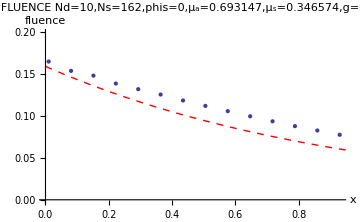

```mathematica
ClearAll[A,y,CoordTbl,nTbl,data,n,pltstr,fluence]
sol2scp=Partition[sol2sc,Nm];
y=0.5;A=Total[area];
CoordTbl=Table[{x,y},{x,0.01,0.99,0.9 √(A/N[Ns])}];
nTbl=PickTriangle/@CoordTbl;
data=Transpose@{CoordTbl⟦All,1⟧,sol2scp⟦nTbl,Nd+1⟧//Re};
For[n=1,n≤Length[data],n++,data⟦n,2⟧+=Exp[-OpticalPathC[CoordTbl⟦n⟧,phis+π]]/(2π);];
pltstr="NEW FLUENCE\n"<>"Nd="<>ToString[Nd]<>",Ns="<>ToString[Ns]<>",phis="<>ToString[phis]<>",μ_a="<>ToString[mua[{0,0}]]<>",μ_s="<>ToString[mus[{0,0}]]<>",g="<>ToString[g]<>",y="<>ToString[y];
Print@Show[
ListPlot[data,PlotRange->{0,1/(2π)+0.04},PlotLabel->pltstr,AxesLabel->{"x","fluence"},PlotStyle->{PointSize[Medium]},ImageSize->Medium],
Plot[Exp[-mut[{0.,0.}]x]/(2π),{x,0,1},PlotStyle->{Red,Dashed,Thick}]
]
fluence=Interpolation[{cntr,sol2scp⟦All,Nd+1⟧32}//Chop//Transpose]//Quiet;
DensityPlot[fluence[x,y]+Exp[-mutTbl⟦1⟧x]/(2π),{x,0,1},{y,0,1},AspectRatio->Automatic,ColorFunction->"SunsetColors",PlotLegends->Automatic,ImageSize->Medium,AxesLabel->{"x","y"}]//Quiet;
```